# :d83d:dcab Day 1: Basic projecting motion and characterizing rotation

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## 3-1-3 rotations

```mathematica
RotationMatrix[ϕ,{0,0,1}]//MatrixForm
```

(Cos[ϕ] | -Sin[ϕ] | 0
Sin[ϕ] | Cos[ϕ] | 0
0 | 0 | 1)

```mathematica
ψ
```

```mathematica
ψ
```

## Projectile Simulation

```mathematica
With[{context="sim`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
ClearAll[x,t,fg,m,g]
initialConditions={x[0]=={0,0},x'[0]=={2,20}}
forces=<|fg->{0,-m g}|>
params=<|m->.10,g->9.8|>
simRange={t,0,3};

diffeqs={(fg==m x''[t])}/.forces/.params
```

{x[0]=={0,0},x'[0]=={2,20}}

<|fg→{0,-g m}|>

<|m→0.1,g→9.8|>

{{0,-0.98}==0.1 x''[t]}

```mathematica
Join[initialConditions,diffeqs]
```

InterpolatingFunction[{{0., 3.}}, <>][t]

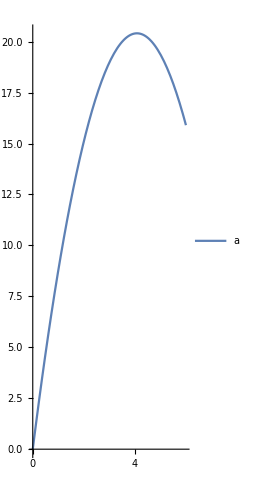

```mathematica
sol=NDSolveValue[Join[initialConditions,diffeqs],x[t],simRange]
ParametricPlot[sol,Evaluate@simRange,PlotLegends->{"a","b"}]
```

```mathematica
With[{context="sim`"},If[Context[]==context,End[],"Not in context"]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
sol/.t->3
```

{6.,15.9}